# Windowed Incremental Online Statistics

## Extracting Models from Data, One Observation at a Time

Brian Beckman

29 March 2019

We calculate descriptive statistics --- mean, unbiased variance, windowed versions of the same --- of abstract sequences of numerical data. Fold and its variants decouple iteration and accumulation from data access. Exactly the same stateless accumulator functions work over data distributed over space --- in memory or in tables, or over time in asynchronous streams. Such functions can be tested independently of data source: over ground-truth test. The same functions can be deployed in harsh asynchronous environments without even being recompiled.

## Prelude: Running Count

For ground truth, we want a fixed but random collection of data. The following is a sample of length ten from the standard normal distribution, mean zero, standard deviation one:

```mathematica
zs = {-0.178654,0.828305,0.0592247,-0.0121089,-1.48014,-0.315044,-0.324796,-0.676357,0.16301,-0.858164};
```

We begin with a trivial exercise to focus attention on the fold rather than on the accumulator function. Note specifically the elegant signature of Fold. There are three arguments: an accumulator function, an initial state, and an abstraction of the sequence of data. All variations of Fold --- over asynchronous streams, lazy streams, tables, lists, arrays --- have exactly the same signature.

```mathematica
ClearAll[cume];
cume[n_,z_]:=n+1;
Fold[cume,0,zs]
```

10

To see all intermediate results, use FoldList:

```mathematica
FoldList[cume,0,zs]
```

{0,1,2,3,4,5,6,7,8,9,10}

LEFT FOLD

Wolfram’s documentation for Fold includes an example that explains this operator symbolically:

```mathematica
Fold[f,z,{a,b,c,d}]
```

f[f[f[f[z,a],b],c],d]

Fold iteratively applies the binary function f to the sequence {a,b,c,d}. Fold places no restriction on its function argument f other than it be binary, accepting an argument of the type of z in its first position, an argument of the type of any of a,b,c,d, in its second position, and producing an result of the same type as z.

RIGHT FOLD

We use only the left fold in this document. Contrast it to the right fold, presented for conceptual completeness:

```mathematica
Fold[{x,y}↦f[y,x],z,{a,b,c,d}]
```

f[d,f[c,f[b,f[a,z]]]]

Operators of the same signature as Fold are broadly useful for separating computation from data access. Wolfram’s Fold works only on lists in memory, but similar fold operators are easy to write over asynchronous and lazy streams. All folds accept exactly the same types of arguments in the same order, including accumulator functions, even without recompiling.

## Running Mean

Write x for the mean-so-far, and write a new accumulator function that computes the running mean.

```mathematica
ClearAll[cume];
cume[{x_,n_,sum_},z_]:=
{(sum+z)/(n+1),n+1,sum+z};
Fold[cume,{0,0,0},zs]
```

{-0.279472,10,-2.79472}

Check against Mathematica built-in.

```mathematica
Mean[zs]
```

-0.279472

Notice how the mean improves as data accumulate, here over a longer and random sample:

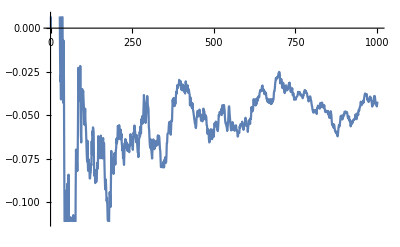

```mathematica
ListLinePlot[#⟦1⟧&/@FoldList[cume,{0,0,0},RandomVariate[NormalDistribution[],1000]]]
```

A preferable form with one fewer quantity to track: new value as sum of old value and a correction that depends only on old values. The right-hand side of the recurrence z̄←z̄+K×(z-z̄) depends only on old values except for the new datum z. The recurrence is not an equation, but it’s shorthand for the following equation, just without the distracting subscripts:

(z̄)_(n+1)=(z̄)_n+K×(z_(n+1)-(z̄)_n)=x+K×(z_(n+1)-x).

```mathematica
ClearAll[cume];
cume[{x_,n_},z_]:=
With[{K=1/(n+1)},
{x+K(z-x),n+1}];
Fold[cume,{0,0},zs]
```

{-0.279472,10}

We prefer this form because (1) it separates old quantities on the right (except for the new datum, z) from new quantities on the left, and (2) it is easy to memorize because it is an affine update: the old estimate plus a correction written as a gain times the residual: the difference between the new observation and the old mean-so-far.

Equation 1 is formally identical to the Kalman update equation. This document builds up to the Kalman filter through more elementary calculations that have similar forms.

The following numerical check proves that we have a correct formula.

```mathematica
ClearAll[cume];
cume[{x_,n_},z_]:=
With[{K=1/(n+1)},
{K(z+n x),n+1}];
Fold[cume,{0,0},zs]
```

{-0.279472,10}

Symbolically, the Kalman-like form x+K(z-x) is equal to the more obvious form (n x+z)/(n+1) when n+1≠ 0.

```mathematica
Solve[x+K(z-x)==(n x+z)/(n+1),K]
```

{{K→1/(1+n)}}

## Running Variance

### Definitions

Variance is the sum of squared residuals with respect to the running mean divided by the count less one. The “count less one” is Bessel’s correction.

```mathematica
Variance[zs]
```

0.395183

Variance is also standard deviation squared.

```mathematica
StandardDeviation[zs]^2==Variance[zs]
```

True

The sum of squared residuals,

Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2

is the variance times the length-less-one:

```mathematica
Variance[zs]*(Length[zs]-1)
```

3.55665

```mathematica
With[{μ=Mean[zs]},
Plus@@((#-μ)^2&/@zs)]
```

3.55665

The covariance, for scalar data, is the same as the Variance. For vector data, the covariance is a matrix.

```mathematica
Covariance[zs]*(Length[zs]-1)
```

3.55665

### Requirement

We require a running variance that does not refer to future observations (even indirectly, through the eventual mean (z̄)_n) and does not store the entire past, only a summary of constant size.

### Brute-Force Variance (doesn’t meet requirements)

The following accumulates variance directly from the definition, useful for numerical checks. However, it assumes we know length and mean of the entire sequence zs ahead of time, so it does not meet the requirement of being incremental. It also needs computer memory for the entire sequence zs, which is of variable or unknown length, so does not meet the requirement of constant memory.

Re-use the variable zs, now for a shorter sequence of ground-truth data.

```mathematica
ClearAll[zs];zs={55,89,144};
```

```mathematica
Variance[zs]//N
```

2017.

```mathematica
ClearAll[cume];
cume[var_,z_]:=var+(z-Mean[zs])^2/(Length[zs]-1);
FoldList[cume,0.,zs]
```

{0.,840.5,865.,2017.}

The intermediate variances are not valid because they do not refer to the “mean-so-far,” but to the final mean.

### School Variance (meets requirements)

The following is much better, exploiting the “school formula,” proved by expanding the square. Letting (z̄)_n=x, incremental running mean, the following yields the sum of squared residuals, ssq:

∑_(i=1)^n (z_i-(z̄)_n)^2=(∑_(i=1)^n z_i^2)-n (z̄)_n^2

Variance is ssq divided by n-1 when n>1. When n=1, variance must be zero because there is no dispersion when there is only one datum. Write:

```mathematica
ClearAll[cume];
cume[{var_,ssq_,x_,n_},z_]:=
With[{n2=n+1},
With[{K=1/n2},
With[{x2=x+K(z-x),ssq2=ssq+z^2},
{(ssq2-n2 x2^2)/Max[1,n],ssq2,x2,n2}]]];
FoldList[cume,{0,0,0,0},zs]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 3025 | 55 | 1
578 | 10946 | 72 | 2
2017 | 31682 | 96 | 3)

The variance computed this way is incremental and runs in constant memory. It tracks three auxiliary quantities: the sum of squares ssq, the mean-so-far x, and the count n. Notice, for the future, that ssq grows quickly, inviting numerical issues.

### Recurrent Variance (meets requirements)

The school variance isn’t a recurrence. A recurrence expresses new variance as a function of the old variance. The function, in our preferred form, is the old variance plus a correction, where the correction depends only on old values. Start with a recurrence for the sum of squared residuals, ssr, Σ_n=^def∑_(i=1)^n (z_i-(z̄)_n)^2:

Σ←Σ+n/(n+1)(z-z̄)^2

The form in equation 4 is an abbreviation for equation 5. The abbreviation is precise under the rule that all accumulated quantities, namely z̄ and Σ, on the right of the recurrence arrow, are old --- have implicit subscript n; only the datum z is new --- with subscript n+1, on the right of the recurrence arrow.

Σ_(n+1)=Σ_n+n/(n+1)(z_(n+1)-(z̄)_n)^2

#### Proof

Here’s the old ssq:

S_n=∑_(i=1)^n z_i^2-n(z̄)_n^2

Here’s the new ssq:

S_(n+1)  =  ∑_(i=1)^(n+1) z_i^2-(n+1)(z̄)_(n+1)^2

Let s z_n^2= sz2[n] be ∑_(i=1)^n z_i^2

```mathematica
ClearAll[s,zb,zbar];
s[n_]:=sz2[n]-n zbar[n]^2
```

```mathematica
rulez$={sz2[1+n]-sz2[n]->z^2,zbar[1+n]->n/(n+1) zbar[n]+z/(n+1)};
```

```mathematica
s[n]//.rulez$
```

sz2[n]-n zbar[n]^2

```mathematica
s[n+1]-s[n]//.rulez$//FullSimplify
```

(n (z-zbar[n])^2)/(1+n)

This is the correction term in the recurrence 4.

By hand, here are rulez$:

s z_(n+1)^2=s z_n^2+z^2

(n+1)(z̄)_(n+1)=n(z̄)_n+z

Expand out the definition of S_(n+1):

S_(n+1)=s z_(n+1)^2-(n+1)(z̄)_(n+1)^2=[s z_n^2+z^2]-(1/(n+1)[(n+1)(z̄)_(n+1)])^2    =    [s z_n^2+z^2]-(1/(n+1)[n(z̄)_n+z])^2

Expand the second term:

S_(n+1)=s z_n^2+z^2-n^2/(n+1)(z̄)_n^2-(2n)/(n+1)z (z̄)_n-1/(n+1)z^2

Add and subtract a term to isolate the prior value of S_n and prepare other terms for cancelation:

=[s z_n^2-n (z̄)_n^2]+n(n+1)/(n+1) (z̄)_n^2+(n+1)/(n+1)z^2-n^2/(n+1)(z̄)_n^2-(2n)/(n+1)z (z̄)_n-1/(n+1)z^2

Cancel terms and complete the square:

=[s z_n^2-n (z̄)_n^2]+n/(n+1) (z̄)_n^2-(2n)/(n+1)z (z̄)_n+n/(n+1)z^2

S_(n+1)=S_n+n/(n+1)(z- (z̄)_n)^2

#### Equivalence to Welford’s

Welford’s famous recurrence is

Σ←Σ+(z-(z̄)_n)(z-(z̄)_(n+1))

where (z̄)_n is the last estimate of the mean and (z̄)_(n+1) is the new or current estimate. The correction term on the right of recurrence 7 is exactly equal to the correction term on the right of recurrence 4.

```mathematica
(z-zbar[n])(z-zbar[n+1]//.rulez$//FullSimplify)
```

(n (z-zbar[n])^2)/(1+n)

We won’t write out the algebraic manipulations, but it’s good practice.

Welford's is easier to memorize than recurrence 4, but its right-hand side depends on both the old mean (z̄)_n and the new mean (z̄)_(n+1), whereas we always want right-hand sides that depend only on old values (except for new datum z) because such right-hand sides require fewer intermediate variables. Notice the following, using Welford’s, has three levels of With because ssr2 depends on two means and we must precompute x2:

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},
With[{x2=x+K(z-x)},
With[{ssr2=(n-1)var+(z-x)(z-x2)},
{ssr2/Max[1,n],x2,n+1}]]];
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

#### Folding It

Recurrence 4 lets us get rid of one level of With, one level of dependency:

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},
With[{x2=x+K(z-x),
ssr2=(n-1) var+K n(z-x)^2},
{ssr2/Max[1,n],x2,n+1}]];
FoldList[cume,{0,0,0},zs]//MatrixForm
```

(0 | 0 | 0
0 | 55 | 1
578 | 72 | 2
2017 | 96 | 3)

#### To LATEX:

```mathematica
ClearAll[cume];
cume[{var_,x_,n_},z_]:=
With[{K=1/(n+1)},
With[{x2=x+K(z-x),
ssr2=(n-1) var+K n(z-x)^2},
{ssr2/Max[1,n],x2,n+1}]];
FoldList[cume,{0,0,0},zs]//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & 55 & 1 \\
 578 & 72 & 2 \\
 2017 & 96 & 3 \\
\end{array}
\right)

## Windowed Statistics

Sometimes, we want the mean and variance of a limited amount of the past, say over a window of length w.

```mathematica
Manipulate[
Grid[Table[With[{l=i-w+1},Piecewise[{{Item[j,Background->LightBlue], j<l}, {Item[j,Background->Yellow], j≤i}, {j, True}}]],{i,n+w},{j,n}],Frame->All],
{{n,10},5+Range[100]},
{{w,3},Range[n+1]-1,Appearance->"Labeled"}]
```

Assume the

Suppose we already have at least w≤n data.

R_(w,n)=∑_(i=n-w+1)^n z_i

S_(w,n)=∑_(i=n-w+1)^n z_i^2-1/w(∑_(i=n-w+1)^n z_i )^2

```mathematica
Module[{data=Table[Subscript[z, i],{i,4}],cume},
cume[{n_,zm1_,x_,v_},z_]:=
{n+1,z,x+1/(n+1)(z-x),
((n-1)v+n/(n+1)(z-x)^2)/Max[1,n]};
Grid[
FoldList[cume,{0,0,0,0},data],Frame->All]]
```

0 | 0 | 0 | 0
1 | z_1 | z_1 | 0
2 | z_2 | z_1+1/2 (-z_1+z_2) | 1/2 (-z_1+z_2)^2
3 | z_3 | z_1+1/2 (-z_1+z_2)+1/3 (-z_1+1/2 (z_1-z_2)+z_3) | 1/2 (1/2 (-z_1+z_2)^2+2/3 (-z_1+1/2 (z_1-z_2)+z_3)^2)
4 | z_4 | z_1+1/2 (-z_1+z_2)+1/3 (-z_1+1/2 (z_1-z_2)+z_3)+1/4 (-z_1+1/2 (z_1-z_2)+1/3 (z_1+1/2 (-z_1+z_2)-z_3)+z_4) | 1/3 (1/2 (-z_1+z_2)^2+2/3 (-z_1+1/2 (z_1-z_2)+z_3)^2+3/4 (-z_1+1/2 (z_1-z_2)+1/3 (z_1+1/2 (-z_1+z_2)-z_3)+z_4)^2)

```mathematica
ClearAll[buttonize];
buttonize[fnRandom_,fnResultFromRandom_,lbl_:"RANDOMIZE!"]:=
DynamicModule[{val=fnRandom[]},
Manipulate[fnResultFromRandom[val],
Button[lbl,val=fnRandom[]]]];
```

```mathematica
buttonize[RandomReal,Identity]
```

```mathematica
((n+1)mn-(n+1-w)ml)/w//FullSimplify
```

ml+((-ml+mn) (1+n))/w

```mathematica
(n υn+(n+1)mn^2-(n-w)υl-(n+1-w)ml^2-w mw^2)/(w-1)//FullSimplify
```

(mn^2 (1+n)-mw^2 w+ml^2 (-1-n+w)-n υl+w υl+n υn)/(-1+w)

#### Data from the C program

```mathematica
Module[{w=3,u,j,mnp1,mjp1,mw,vnp1,vjp1,vw,cbuf,zj,
data={0.857454,0.312454,0.705325,0.839363,1.63781,0.699257,-0.340016,-0.213596,-0.0418609,0.054705},cume},
cbuf=ConstantArray[0,w];
cume[{_,n_,_,_,_,mn_,mj_,_,_,_,vn_,vj_,_,_,_},z_]:=(
zj=cbuf⟦w⟧;     cbuf=RotateRight[cbuf,1];    cbuf⟦1⟧=z;
j=Max[0,n-w+1];     u=n-j+1;
mnp1=mn+(z-mn)/(n+1);
mjp1=If[j>0,mj+(zj-mj)/j,0];
mw=((n+1)mnp1-j mjp1)/u;
vnp1=((n-1)vn+n/(n+1)(z-mn)^2)/Max[1,n];
vjp1=If[j>1,(j-2)/(j-1)vj+1/j(zj-mj)^2,0];
vw=(n vnp1-(n-w)vjp1+(n+1)mnp1^2-j mjp1^2-u mw^2)/Max[1,u-1];
{j,n+1,u,z,zj,(* THIS IS THE RETURN VALUE *)
mnp1,mjp1,If[j>0,Mean[data⟦1;;j⟧],0],
mw,Mean[data⟦j+1;;n+1⟧],
vnp1,vjp1,If[j>1,Variance[data⟦1;;j⟧],0],
vw,If[u>1,Variance[data⟦j+1;;n+1⟧],0]});
Grid[
Prepend[FoldList[cume,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},data],
{"j","n+1","u","z","z_j","μ'","μ'_j","chk μ'_j","μ'_w","chk μ'_w","υ'","υ'_j","chk υ'_j","υ'_w","chk υ'_w"}],Frame->All]]
```

j | n+1 | u | z | z_j | μ' | μ'_j | chk μ'_j | μ'_w | chk μ'_w | υ' | υ'_j | chk υ'_j | υ'_w | chk υ'_w
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0.857454 | 0 | 0.857454 | 0 | 0 | 0.857454 | 0.857454 | 0. | 0 | 0 | 0. | 0
0 | 2 | 2 | 0.312454 | 0 | 0.584954 | 0 | 0 | 0.584954 | 0.584954 | 0.148513 | 0 | 0 | 0.148513 | 0.148513
0 | 3 | 3 | 0.705325 | 0 | 0.625078 | 0 | 0 | 0.625078 | 0.625078 | 0.079086 | 0 | 0 | 0.079086 | 0.079086
1 | 4 | 3 | 0.839363 | 0.857454 | 0.678649 | 0.857454 | 0.857454 | 0.619047 | 0.619047 | 0.0642035 | 0 | 0 | 0.0749912 | 0.0749912
2 | 5 | 3 | 1.63781 | 0.312454 | 0.870481 | 0.584954 | 0.584954 | 1.06083 | 1.06083 | 0.232151 | 0.148513 | 0.148513 | 0.254169 | 0.254169
3 | 6 | 3 | 0.699257 | 0.705325 | 0.841944 | 0.625078 | 0.625078 | 1.05881 | 1.05881 | 0.190607 | 0.079086 | 0.079086 | 0.256338 | 0.256338
4 | 7 | 3 | -0.340016 | 0.839363 | 0.673092 | 0.678649 | 0.678649 | 0.665684 | 0.665684 | 0.358415 | 0.0642035 | 0.0642035 | 0.978794 | 0.978794
5 | 8 | 3 | -0.213596 | 1.63781 | 0.562256 | 0.870481 | 0.870481 | 0.0485483 | 0.0485483 | 0.40549 | 0.232151 | 0.232151 | 0.321562 | 0.321562
6 | 9 | 3 | -0.0418609 | 0.699257 | 0.495132 | 0.841944 | 0.841944 | -0.198491 | -0.198491 | 0.395354 | 0.190607 | 0.190607 | 0.0223952 | 0.0223952
7 | 10 | 3 | 0.054705 | -0.340016 | 0.45109 | 0.673092 | 0.673092 | -0.0669173 | -0.0669173 | 0.370824 | 0.358415 | 0.358415 | 0.0184672 | 0.0184672

#### Window 6

```mathematica
Module[{w=6,u,j,mnp1,mjp1,mw,vnp1,vjp1,vw,cbuf,zj,
data={0.857454,0.312454,0.705325,0.839363,1.63781,0.699257,-0.340016,-0.213596,-0.0418609,0.054705,1.10464,-0.387322,-0.00175018,1.12034,0.280948,-1.07877},cume},
cbuf=ConstantArray[0,w];
cume[{_,n_,_,_,_,mn_,mj_,_,_,_,vn_,vj_,_,_,_},z_]:=(
zj=cbuf⟦w⟧;     cbuf=RotateRight[cbuf,1];    cbuf⟦1⟧=z;
j=Max[0,n-w+1];     u=n-j+1;
mnp1=mn+(z-mn)/(n+1);
mjp1=If[j>0,mj+(zj-mj)/j,0];
mw=((n+1)mnp1-j mjp1)/u;
vnp1=((n-1)vn+n/(n+1)(z-mn)^2)/Max[1,n];
vjp1=If[j>1,(j-2)/(j-1)vj+1/j(zj-mj)^2,0];
vw=(n vnp1-(n-w)vjp1+(n+1)mnp1^2-j mjp1^2-u mw^2)/Max[1,u-1];
{j,n+1,u,z,zj,(* THIS IS THE RETURN VALUE *)
mnp1,mjp1,If[j>0,Mean[data⟦1;;j⟧],0],
mw,Mean[data⟦j+1;;n+1⟧],
vnp1,vjp1,If[j>1,Variance[data⟦1;;j⟧],0],
vw,If[u>1,Variance[data⟦j+1;;n+1⟧],0]});
Grid[
Prepend[FoldList[cume,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},data],
{"j","n+1","u","z","z_j","μ_(n + 1)","μ_j","μ'_j","μ_w","μ'_w","υ_(n + 1)","υ_j","υ'_j","υ_w","υ'_w"}],Frame->All]]
```

j | n+1 | u | z | z_j | μ_(n + 1) | μ_j | μ'_j | μ_w | μ'_w | υ_(n + 1) | υ_j | υ'_j | υ_w | υ'_w
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0.857454 | 0 | 0.857454 | 0 | 0 | 0.857454 | 0.857454 | 0. | 0 | 0 | 0. | 0
0 | 2 | 2 | 0.312454 | 0 | 0.584954 | 0 | 0 | 0.584954 | 0.584954 | 0.148513 | 0 | 0 | 0.148513 | 0.148513
0 | 3 | 3 | 0.705325 | 0 | 0.625078 | 0 | 0 | 0.625078 | 0.625078 | 0.079086 | 0 | 0 | 0.079086 | 0.079086
0 | 4 | 4 | 0.839363 | 0 | 0.678649 | 0 | 0 | 0.678649 | 0.678649 | 0.0642035 | 0 | 0 | 0.0642035 | 0.0642035
0 | 5 | 5 | 1.63781 | 0 | 0.870481 | 0 | 0 | 0.870481 | 0.870481 | 0.232151 | 0 | 0 | 0.232151 | 0.232151
0 | 6 | 6 | 0.699257 | 0 | 0.841944 | 0 | 0 | 0.841944 | 0.841944 | 0.190607 | 0 | 0 | 0.190607 | 0.190607
1 | 7 | 6 | -0.340016 | 0.857454 | 0.673092 | 0.857454 | 0.857454 | 0.642365 | 0.642366 | 0.358415 | 0 | 0 | 0.422167 | 0.422167
2 | 8 | 6 | -0.213596 | 0.312454 | 0.562256 | 0.584954 | 0.584954 | 0.554691 | 0.554691 | 0.40549 | 0.148513 | 0.148513 | 0.537708 | 0.537708
3 | 9 | 6 | -0.0418609 | 0.705325 | 0.495132 | 0.625078 | 0.625078 | 0.43016 | 0.43016 | 0.395354 | 0.079086 | 0.079086 | 0.585735 | 0.585735
4 | 10 | 6 | 0.054705 | 0.839363 | 0.45109 | 0.678649 | 0.678649 | 0.299383 | 0.299383 | 0.370824 | 0.0642035 | 0.0642035 | 0.559916 | 0.559916
5 | 11 | 6 | 1.10464 | 1.63781 | 0.510503 | 0.870481 | 0.870481 | 0.210522 | 0.210522 | 0.372571 | 0.232151 | 0.232151 | 0.321851 | 0.321851
6 | 12 | 6 | -0.387322 | 0.699257 | 0.435684 | 0.841944 | 0.841944 | 0.029425 | 0.029425 | 0.405875 | 0.190607 | 0.190607 | 0.306206 | 0.306206
7 | 13 | 6 | -0.00175018 | -0.340016 | 0.402036 | 0.673092 | 0.673092 | 0.0858027 | 0.0858027 | 0.386771 | 0.358415 | 0.358415 | 0.275289 | 0.275289
8 | 14 | 6 | 1.12034 | -0.213596 | 0.453343 | 0.562256 | 0.562256 | 0.308125 | 0.308125 | 0.393874 | 0.40549 | 0.40549 | 0.412102 | 0.412102
9 | 15 | 6 | 0.280948 | -0.0418609 | 0.44185 | 0.495132 | 0.495132 | 0.361927 | 0.361927 | 0.367722 | 0.395354 | 0.395354 | 0.384278 | 0.384278
10 | 16 | 6 | -1.07877 | 0.054705 | 0.346811 | 0.45109 | 0.45109 | 0.173014 | 0.173014 | 0.487725 | 0.370824 | 0.370824 | 0.737697 | 0.737697

#### Window 3, Random Data

```mathematica
Module[{w=3,u,j,mnp1,mjp1,mw,vnp1,vjp1,vw,cbuf,zj,
data=N@RandomInteger[{-100,100},16],cume},
cbuf=ConstantArray[0,w];
cume[{_,n_,_,_,_,mn_,mj_,_,_,_,vn_,vj_,_,_,_},z_]:=(
zj=cbuf⟦w⟧;     cbuf=RotateRight[cbuf,1];    cbuf⟦1⟧=z;
j=Max[0,n-w+1];     u=n-j+1;
mnp1=mn+(z-mn)/(n+1);
mjp1=If[j>0,mj+(zj-mj)/j,0];
mw=((n+1)mnp1-j mjp1)/u;
vnp1=((n-1)vn+n/(n+1)(z-mn)^2)/Max[1,n];
vjp1=If[j>1,(j-2)/(j-1)vj+1/j(zj-mj)^2,0];
vw=(n vnp1-(n-w)vjp1+(n+1)mnp1^2-j mjp1^2-u mw^2)/Max[1,u-1];
{j,n+1,u,z,zj,(* THIS IS THE RETURN VALUE *)
mnp1,mjp1,If[j>0,Mean[data⟦1;;j⟧],0],
mw,Mean[data⟦j+1;;n+1⟧],
vnp1,vjp1,If[j>1,Variance[data⟦1;;j⟧],0],
vw,If[u>1,Variance[data⟦j+1;;n+1⟧],0]});
Grid[
Prepend[FoldList[cume,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},data],
{"j","n+1","u","z","z_j","μ_(n + 1)","μ_j","μ'_j","μ_w","μ'_w","υ_(n + 1)","υ_j","υ'_j","υ_w","υ'_w"}],Frame->All]]
```

j | n+1 | u | z | z_j | μ_(n + 1) | μ_j | μ'_j | μ_w | μ'_w | υ_(n + 1) | υ_j | υ'_j | υ_w | υ'_w
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | -20. | 0 | -20. | 0 | 0 | -20. | -20. | 0. | 0 | 0 | 0. | 0
0 | 2 | 2 | 45. | 0 | 12.5 | 0 | 0 | 12.5 | 12.5 | 2112.5 | 0 | 0 | 2112.5 | 2112.5
0 | 3 | 3 | -94. | 0 | -23. | 0 | 0 | -23. | -23. | 4837. | 0 | 0 | 4837. | 4837.
1 | 4 | 3 | -63. | -20. | -33. | -20. | -20. | -37.3333 | -37.3333 | 3624.67 | 0 | 0 | 5324.33 | 5324.33
2 | 5 | 3 | 82. | 45. | -10. | 12.5 | 12.5 | -25. | -25. | 5363.5 | 2112.5 | 2112.5 | 8827. | 8827.
3 | 6 | 3 | 64. | -94. | 2.33333 | -23. | -23. | 27.6667 | 27.6667 | 5203.47 | 4837. | 4837. | 6246.33 | 6246.33
4 | 7 | 3 | 10. | -63. | 3.42857 | -33. | -33. | 52. | 52. | 4344.62 | 3624.67 | 3624.67 | 1404. | 1404.
5 | 8 | 3 | -76. | 82. | -6.5 | -10. | -10. | -0.666667 | -0.666667 | 4512.57 | 5363.5 | 5363.5 | 4985.33 | 4985.33
6 | 9 | 3 | -21. | 64. | -8.11111 | 2.33333 | 2.33333 | -29. | -29. | 3971.86 | 5203.47 | 5203.47 | 1897. | 1897.
7 | 10 | 3 | -94. | 10. | -16.7 | 3.42857 | 3.42857 | -63.6667 | -63.6667 | 4268.23 | 4344.62 | 4344.62 | 1446.33 | 1446.33
8 | 11 | 3 | -53. | -76. | -20. | -6.5 | -6.5 | -56. | -56. | 3961.2 | 4512.57 | 4512.57 | 1339. | 1339.
9 | 12 | 3 | 35. | -21. | -15.4167 | -8.11111 | -8.11111 | -37.3333 | -37.3333 | 3853.17 | 3971.86 | 3971.86 | 4344.33 | 4344.33
10 | 13 | 3 | 82. | -94. | -7.92308 | -16.7 | -16.7 | 21.3333 | 21.3333 | 4262.08 | 4268.23 | 4268.23 | 4696.33 | 4696.33
11 | 14 | 3 | 10. | -53. | -6.64286 | -20. | -20. | 42.3333 | 42.3333 | 3957.17 | 3961.2 | 3961.2 | 1336.33 | 1336.33
12 | 15 | 3 | 94. | 35. | 0.0666667 | -15.4167 | -15.4167 | 62. | 62. | 4349.78 | 3853.17 | 3853.17 | 2064. | 2064.
13 | 16 | 3 | 27. | 82. | 1.75 | -7.92308 | -7.92308 | 43.6667 | 43.6667 | 4105.13 | 4262.08 | 4262.08 | 1972.33 | 1972.33

```mathematica
DynamicModule[{w=3,u,l,mn,ml,mw,υn,υl,υw,data=N@RandomInteger[{-100,100},10],cume},
cume[{_,n_,_,_,x_,xw_,_,_,v_,vw_,_,_},z_]:=(
(* n : how many points seen before this one. *)
(* z : current data point, at index n + 1. *)
(* l : index of first point in window at least 1 wide and no more than w wide. *)
(* w : width of window. *)
(* u : number of points including z in the running window; converges to w. *)
(* mn : the mean of all points through Subscript[z, n+1]. *)
(* ml : the mean of all points through index l-1 = n+1-w, lagging w behind mn. *)
(* mw : the mean of all points within the window. *)
(* υn : variance of all points through Subscript[z, n+1]. *)
(* υl : variance of all points through index l-1 = n+1-w, lagging w behind υn *)
(* υw : variance of all points within the window. *)

l=Max[1,n-w+2];
mn=x+(z-x)/(n+1);
ml=If[n+1>w,xw+(data⟦n+1-w⟧-xw)/(n+1-w),0];
mw=((n+1)mn-(n+1-w)ml)/w;
υn=((n-1)v+n/(n+1)(z-x)^2)/Max[1,n];
υl=If[n+1>w,((n-w-1)υl+(n-w)/(n-w+1)(data⟦n+1-w⟧-xw)^2)/Max[1,n-w],0];
υw=(n υn+(n+1)mn^2-(n-w)υl-(n+1-w)ml^2-w mw^2)/(w-1);
{l,n+1,n+2-l,z,
mn,ml,mw,Mean[data⟦l;;n+1⟧],υn,υl,υw,Quiet@Variance[data⟦l;;n+1⟧]});
Manipulate[Grid[
Prepend[FoldList[cume,{0,0,0,0,0,0,0,0,0,0,0,0},data],
{"l","n+1","u","z","μ_(n + 1)","μ_l","μ_w","μ'_w","υ_(n + 1)","υ_l","υ_w","υ'_w"}],Frame->All],
Button["RANDOMIZE!",data=N@RandomInteger[{-100,100},10]]]]
```